```mathematica
betas=ToString[NumberForm[#,{1,1}]]&/@{0.0,0.5,1.0};
mus=ToString[NumberForm[#,{1,1}]]&/@{0.7,0.8,0.9,1.0};
```

```mathematica
root="/Users/matt/wsu/old-livestock/livestock-agent-model/frontiers_ensemble";
```

```mathematica
betamus=Table[Table[{betas[[b]],mus[[m]]},{b,1,3}],{m,1,4}]
```

{{{0.0,0.7},{0.5,0.7},{1.0,0.7}},{{0.0,0.8},{0.5,0.8},{1.0,0.8}},{{0.0,0.9},{0.5,0.9},{1.0,0.9}},{{0.0,1.0},{0.5,1.0},{1.0,1.0}}}

```mathematica
prefix={"a","b","c","d","e","f","g","h","i","j","k","l"};
curprefix=1;
```

```mathematica
totalPlot[betamu_]:=Module[{data,fname,beta,mu,pfx},
beta=betamu[[1]];
mu=betamu[[2]];
fname=root<>"/output_b"<>beta<>"_m"<>mu<>"/total_animals.csv";
data=Import[fname,"CSV"];
data=(Total[data]/Dimensions[data][[1]]);
pfx=prefix[[curprefix]];
curprefix=curprefix+1;
ListPlot[
Table[{i,data[[i]]},{i,52*5,Length[data]}],
PlotRange->{0,500},
Joined->True,
PlotLabel->"("<>pfx<>")  β="<>beta<>" μ="<>mu,
AxesLabel->{"Time (weeks)","No. of animals"},
ImagePadding->{{30,Automatic},{Automatic,Automatic}}
]
]
```

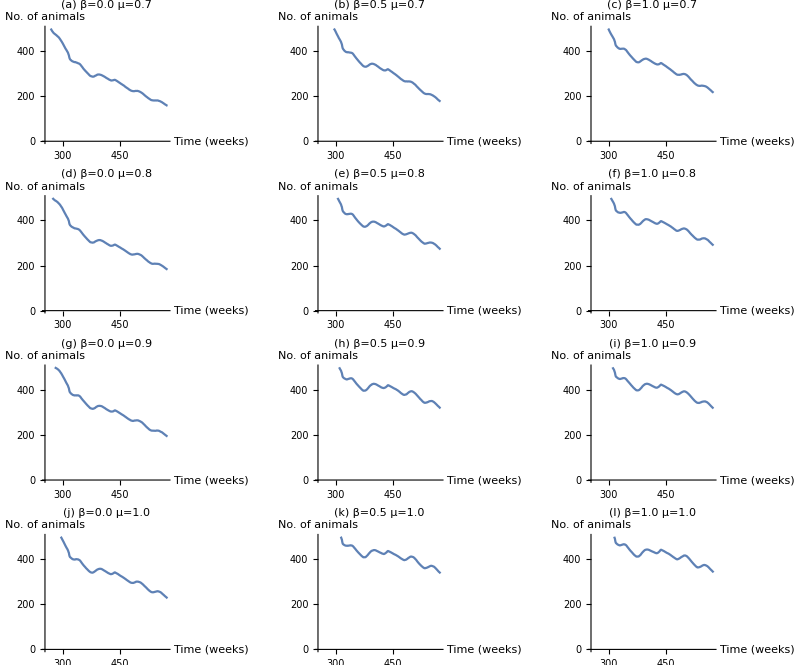

```mathematica
Map[totalPlot,betamus,{2}]//GraphicsGrid[#,Frame->True,ImageSize->800]&
```

```mathematica
prefix={"a","b","c","d","e","f","g","h","i","j","k","l"};
curprefix=1;
```

```mathematica
decisionPlot[betamu_]:=Module[{fname,rvfdata,rvfavg,cbppdata,cbppavg,beta,mu,pfx},
beta=betamu[[1]];
mu=betamu[[2]];
fname=root<>"/output_b"<>beta<>"_m"<>mu<>"/rvf_decisions.csv";
rvfdata=Import[fname,"CSV"];
rvfavg=Total[rvfdata]/Dimensions[rvfdata][[1]];
fname=root<>"/output_b"<>beta<>"_m"<>mu<>"/cbpp_decisions.csv";
cbppdata=Import[fname,"CSV"];
cbppavg=Total[cbppdata]/Dimensions[cbppdata][[1]];
pfx=prefix[[curprefix]];
curprefix=curprefix+1;

BarChart[
{#*5+5&/@rvfavg,#*5+5&/@cbppavg}//Transpose,
ChartLegends->{"RVF","CBPP"},
PlotRange->{0,10},
AxesLabel->{"Year","S=+1 Count"},
ChartLabels->{Table[i,{i,1,Length[rvfavg]}],None},
PlotLabel->"("<>pfx<>")  β="<>beta<>" μ="<>mu,
ImagePadding->{{Automatic,Automatic},{40,Automatic}}
]
];
```

```mathematica
fig=Graphics[Map[decisionPlot,betamus,{2}]//GraphicsGrid[#,Frame->All,ImageSize->800]&]
```

-Graphics-

```mathematica
fig
```

-Graphics-

```mathematica
stats[betamu_]:=Module[{fname,data,beta,mu},
beta=betamu[[1]];
mu=betamu[[2]];
fname=root<>"/output_b"<>beta<>"_m"<>mu<>"/stats.csv";
data=Import[fname,"CSV"];
data=data[[2;;]];
Total[data]/Dimensions[data][[1]]//N
];
```

```mathematica
Map[stats[#][[1]]&,betamus,{2}]//TableForm
```

1631.28 | 1710.1 | 1734.7
1661.68 | 1761.16 | 1780.3
1675.92 | 1799.68 | 1804.96
1703.44 | 1818.74 | 1824.44